# NG^4 T_14.Генетическое кодирование, генетические операции

Шклярик Вера
09-май-2023

## Section. Фенотип

```mathematica
SetDirectory@NotebookDirectory[]
Get["NG23T14Problem.mx","NG23T14"]
```

C:\Users\asus\Desktop\НСиГА\лаб14

Set::wrsym: Symbol Troubles is Protected.

Attributes::locked: Symbol Troubles is locked.

## Section. Квантование

```mathematica
{{0,100},{0,100},{0,10},{0,359}}
{0.1, 0.1, 0.01, 1.}
#2 - #1&@@@%%
%/%%
Ceiling@Log2@%
2^%
```

{{0,100},{0,100},{0,10},{0,359}}

{0.1,0.1,0.01,1.}

{100,100,10,359}

{1000.,1000.,1000.,359.}

{10,10,10,9}

{1024,1024,1024,512}

```mathematica
With[{from = 0, to = 359, bits = 9},Min[2^bits-1,Floor[(#- from)/(to - from)2^bits]]&]
#->%@#&/@{0,0.5,2,2.1,358,358.7,359}
```

Min[2^9-1,Floor[((#1-0) 2^9)/(359-0)]]&

{0→0,0.5→0,2→2,2.1→2,358→510,358.7→511,359→511}

```mathematica
ClearAll[AnalogToDigital,DigitalToAnalog];
AnalogToDigital[{from_,to_},bits_Integer]:=With[{$ = Min[2^bits-1,N@Floor[(#- from)/(to - from)2^bits]]}, $&];
DigitalToAnalog[{from_,to_},bits_Integer]:=With[{$ =from+(#+ 0.5) 2^-bits (to - from)//Expand//N},$&];
```

```mathematica
0.1
AnalogToDigital[{0,100},10]
%@%%
DigitalToAnalog[{0,100},10]
%@%%
% - %%%%%
```

0.1

Min[1023,Floor[10.24 #1]]&

1

0.0488281+0.0976563 #1&

0.146484

0.0464844

## Section. Код Грея

```mathematica
{{0},{1}}
Join[Prepend[#,0]&/@%,Prepend[#,0]&/@Reverse@%]
```

{{0},{1}}

{{0,0},{0,1},{0,1},{0,0}}

```mathematica
Nest[Join["0"<>#&/@#,"1"<>#&/@Reverse@#]&,{"0","1"},9];
%//Dimensions
```

{1024}

```mathematica
ClearAll[GrayTable,ToGray,FromGray];
GrayTable= Nest[Join["0"<>#&/@#,"1"<>#&/@Reverse@#]&,{"0","1"},9];
FromGray[g_String]:= Position[GrayTable,StringPadLeft[g,10,"0"]][[1,1]]-1;
ToGray[n_Integer]:= GrayTable[[n+1]];
ToGray[n_Integer,len_Integer:10]:=StringPadLeft[ GrayTable[[n+1]], len];
```

```mathematica
ToGray[23]
```

0000011100

```mathematica
ToGray[23,6]
```

011100

```mathematica
FromGray[%]
```

23

```mathematica
GrayTable[[11]]
```

0000001111

```mathematica
"10000"
Position[GrayTable,StringPadLeft[%,10,"0"]][[1,1]]-1
```

10000

31

## Section. Генетическое кодирование

```mathematica
ClearAll[ptg, gtp];
ptg[to_, atg_,gb_, X_]:=ToGray[AnalogToDigital[{0,to},atg]@X, gb]
gtp[to_, dta_, X_]:=DigitalToAnalog[{0,to}, dta]@FromGray[X]
```

```mathematica
ptg[10, 10,10, 9.359085419324504]
gtp[10,10,%]
```

1001100001

9.36035

```mathematica
ClearAll[PhenotypeToGenotype,GenotypeToPhenotype];
PhenotypeToGenotype[{x_,y_,F_,α_}]:=ptg[100,10,10,x]<>ptg[100,10,10,y] <>ptg[10,10,10,F] <>ptg[360,9,9,α];
GenotypeToPhenotype[chromosome_String]:=With[{x = StringTake[chromosome, 10], y = StringTake[chromosome,{11,20}], F =StringTake[chromosome, {21,30}], α = StringTake[chromosome,{31,39}] },{gtp[100,10,x], gtp[100,10,y], gtp[10,10,F], gtp[360,9,α]}];
```

```mathematica
PhenotypeToGenotype[{95.69770754669939,26.869518758331967,4.258385911744842,279.58197490794936}]
StringLength[%]
GenotypeToPhenotype[%%]
```

100011101001100110100101101110101001011

39

{95.6543,26.9043,4.2627,279.492}

## Section. Популяция

```mathematica
RandomReal[#,20]&/@{100,100,10,360};
ph = %ᵀ
```

{{30.0778,56.5489,9.3687,265.889},{53.8513,0.0718729,2.72914,234.004},{33.7427,17.0883,9.21968,312.252},{42.3831,15.2359,4.54005,330.125},{49.2493,25.5271,3.2603,28.1741},{90.3268,61.3364,2.07733,197.958},{27.6187,74.1858,2.73412,255.229},{12.9007,62.5708,3.38395,12.484},{64.3947,8.12907,6.66203,111.866},{26.987,46.1932,4.14375,249.492},{70.0975,19.4289,7.4771,240.678},{97.5288,98.3669,3.56484,259.895},{3.93755,44.6428,2.01791,321.556},{56.7461,66.8318,1.25456,218.351},{98.8947,25.1451,4.81359,85.3676},{67.4751,94.3169,1.32774,242.745},{42.7345,70.9939,5.32132,172.213},{3.52248,30.8455,0.826371,6.04064},{38.2112,83.2148,1.1129,229.062},{59.6881,98.71,4.90173,103.947}}

```mathematica
gen = PhenotypeToGenotype/@ph
```

{011010101011011000101001100000111000111,110011010000000000000110011100111101010,011111010100111110011001101000101100010,010110101100110100100100111000100111111,010000010001100001110111101011000111100,100101001011010011100010111110110010101,011001011111100011000110011100111011111,001100011011110000000111110111000011001,111101101000011110101111111111011010000,011001111001001101010101111100111010011,111010101100101001011110000011111111101,100001010110000110000111011011111001001,000011110001001011010010101001100101101,110110011111111110100011000000110101101,100000111001100000010100011010001000101,111110101110001001110011000100111110101,010110111111101111011100110000010001110,000011011001101001100001111110000001100,010100010010111111100001001001111100111,110101001010000010110100001111011011010}

```mathematica
ShowGenotype[gen_]:=ArrayPlot[Characters@gen/.{"0"->Black,"1"->White}]
```

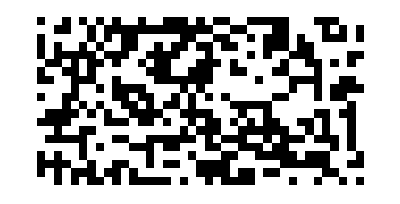

```mathematica
ShowGenotype@gen
```

## Section. Мутация

```mathematica
ClearAll[GenOper];
GenOper["Mutation", individual_String]:=With[{int = RandomInteger[{1,39}]},StringReplacePart[individual,If[StringPart[individual,int]=="0","1","0"],{int, int} ]]
```

```mathematica
Dynamic[ShowGenotype@gen]
n = 10;
Do[gen[[n]]=GenOper["Mutation", gen[[n]]]; n = RandomInteger[{1,20}];,50000]
```

## Section. Инверсия

```mathematica
ClearAll[GenOper];
GenOper["Mutation", individual_String]:=With[{int = RandomInteger[{1,39}]},StringReplacePart[individual,If[StringPart[individual,int]=="0","1","0"],{int, int} ]];
GenOper["Inversion",individual_String]:=StringRotateLeft[individual, RandomInteger[{1,39}]]
```

```mathematica
Dynamic[ShowGenotype@gen]
n = 10;
Do[gen[[n]]=GenOper["Inversion", gen[[n]]]; n = RandomInteger[{1,20}];,200000]
```

## Section. Скрещивание

```mathematica
ClearAll[GenOper];
GenOper["Mutation", individual_String]:=With[{int = RandomInteger[{1,39}]},StringReplacePart[individual,If[StringPart[individual,int]=="0","1","0"],{int, int} ]];
GenOper["Inversion",individual_String]:=StringRotateLeft[individual, RandomInteger[{1,39}]];
GenOper["Crossover", {parent1_String, parent2_String}]:=With[{int = RandomInteger[{1,39}]},StringTake[parent1,int]<>StringTake[parent2,int-39]]
```

```mathematica
GenOper["Crossover", {gen[[3]], gen[[4]]}]//StringLength
```

39

```mathematica
RandomReal[#,20]&/@{100,100,10,360};
ph = %ᵀ;
gen = PhenotypeToGenotype/@ph;
```

```mathematica
Dynamic[ShowGenotype@gen]
n = 10;
m = 11;
Do[gen[[n]]=GenOper["Crossover",{gen[[n]], gen[[m]]}];n = RandomInteger[{1,20}]; m =First@RandomSample[Cases[Range[1,20], Except[n]],1];,500]
```